# Basic functions and definitions

## Basic Definitions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Quiet[Needs["ErrorBarPlots`"]]
```

```mathematica
pr[list_,c_]:=Table[list⟦i⟧⟦c⟧,{i,1,Length[list]}]
```

```mathematica
resolution={1024,1024};
```

## Data Extraction Functions

### Get the average data from data in files

```mathematica
GetFileData[fileName_,fileType_]:=If[FileExistsQ[fileName<>"/number.csv"],({
num=Import[fileName<>"/number.csv"]⟦1⟧⟦1⟧,
data={},
name=fileName<>"/"<>fileType,
For[i=1,i≤num,++i,If[FileExistsQ[name<>ToString[i]<>".csv"],AppendTo[data,Import[name<>ToString[i]<>".csv"]],Null]],
Table[{data⟦1⟧⟦j⟧⟦1⟧,Sum[data⟦i⟧⟦j⟧⟦2⟧,{i,1,Length[data]}]/Length[data]},{j,1,Length[data⟦1⟧]}]
})⟦5⟧,{}]
```

### Get the sample standard deviation of data - divide by N-1

```mathematica
GetFileError[fileName_,fileType_]:=If[FileExistsQ[fileName<>"/number.csv"],({
num=Import[fileName<>"/number.csv"]⟦1⟧⟦1⟧,
data={},
name=fileName<>"/"<>fileType,
For[i=1,i≤num,++i,If[FileExistsQ[name<>ToString[i]<>".csv"],AppendTo[data,Import[name<>ToString[i]<>".csv"]],Null]],

ave=GetFileData[fileName,fileType],
Table[{data⟦1⟧⟦j⟧⟦1⟧,(Sum[(data⟦i⟧⟦j⟧⟦2⟧-ave⟦j⟧⟦2⟧)^2,{i,1,Length[data]}]/(Length[data]-1))^(1/2)},{j,1,Length[data⟦1⟧]}]
})⟦6⟧,{}]
```

### Create data for a ListErrorPlot

```mathematica
GetFileDataWithError[fileName_,fileType_]:=({
g1=GetFileData[fileName,fileType];,
g2=GetFileError[fileName,fileType];,
Partition[Riffle[pr[g1,2],pr[g2,2]],2]
})⟦3⟧
```

### Get good plot limits for list error plots

```mathematica
PlotLimits[dataErrorList_,rounding_]:=({
mn=Min[Table[dataErrorList⟦i⟧⟦1⟧-dataErrorList⟦i⟧⟦2⟧,{i,1,Length[dataErrorList]}]],
mx=Max[Table[dataErrorList⟦i⟧⟦1⟧+dataErrorList⟦i⟧⟦2⟧,{i,1,Length[dataErrorList]}]],
mn-rounding(mx-mn),
mx+rounding(mx-mn)
})⟦3;;4⟧
```

## Special error plotting functions

## For plotting (x,y) data with error strips

```mathematica
ClearAll[GetRange,plusMinusMean,Process,ListPlotSingleError,ListPlotError]
```

```mathematica
DefaultColors=Table[RandomColor[],{i,1,100}];
```

```mathematica
GetRange[data_,sigmas_]:=({
mn=Min[Table[Min[Table[data⟦i⟧⟦j⟧⟦2⟧-sigmas⟦i⟧⟦j⟧⟦2⟧,{j,1,Length[sigmas⟦i⟧]}]],{i,1,Length[data]}]],
mx=Max[Table[Max[Table[data⟦i⟧⟦j⟧⟦2⟧+sigmas⟦i⟧⟦j⟧⟦2⟧,{j,1,Length[sigmas⟦i⟧]}]],{i,1,Length[data]}]],
mn-0.05(mx-mn),
mx+0.05(mx-mn)
})⟦3;;4⟧
```

```mathematica
plusMinusMean[data_,sigma_]:=Transpose[Map[{#⟦1⟧+#⟦2⟧,#⟦1⟧-#⟦2⟧,#⟦1⟧}&,Transpose[{data,sigma}]]]
```

```mathematica
Process[data_,sigma_]:=MapThread[{#1,#2}&,{pr[data,1],#}]&/@plusMinusMean[pr[data,2],pr[sigma,2]]
```

```mathematica
Options[ListPlotSingleError]=Options[ListPlot];
ListPlotSingleError[data_,sigma_,range_:All,opts:OptionsPattern[]]:=
ListPlot[
Process[data,sigma],
Joined->True,
PlotStyle->{Opacity[0],Opacity[0],
If[Length[OptionValue[PlotStyle]]≥i,OptionValue[PlotStyle]⟦i⟧,DefaultColors⟦i⟧]
},
Filling->{1->{2}},
FillingStyle->Directive[Opacity[0.2],
If[Length[OptionValue[PlotStyle]]≥i,OptionValue[PlotStyle]⟦i⟧,DefaultColors⟦i⟧]],
PlotRange->range,
Evaluate[FilterRules[{opts}, Options[ListPlot]]]]
```

```mathematica
ListPlotError[data_,sigmas_,opts:OptionsPattern[]]:=Show[Table[ListPlotSingleError[data⟦i⟧,sigmas⟦i⟧,GetRange[data,sigmas],opts],{i,1,Length[data]}]]
```

# Get data for T=0

#### Get data

```mathematica
pdt03=GetFileData["PvNP_tau0.03_num5000_vel1","PDiff"];
gdt03=GetFileData["PvNP_tau0.03_num5000_vel1","GDiff"];
pdt05=GetFileData["PvNP_tau0.05_num5000_vel1","PDiff"];
gdt05=GetFileData["PvNP_tau0.05_num5000_vel1","GDiff"];
pdt08=GetFileData["PvNP_tau0.08_num5000_vel1","PDiff"];
gdt08=GetFileData["PvNP_tau0.08_num5000_vel1","GDiff"];
pdt10=GetFileData["PvNP_tau0.1_num5000_vel1","PDiff"];
gdt10=GetFileData["PvNP_tau0.1_num5000_vel1","GDiff"];
```

#### Get error

```mathematica
pdt03e=GetFileError["PvNP_tau0.03_num5000_vel1","PDiff"];
gdt03e=GetFileError["PvNP_tau0.03_num5000_vel1","GDiff"];
pdt05e=GetFileError["PvNP_tau0.05_num5000_vel1","PDiff"];
gdt05e=GetFileError["PvNP_tau0.05_num5000_vel1","GDiff"];
pdt08e=GetFileError["PvNP_tau0.08_num5000_vel1","PDiff"];
gdt08e=GetFileError["PvNP_tau0.08_num5000_vel1","GDiff"];
pdt10e=GetFileError["PvNP_tau0.1_num5000_vel1","PDiff"];
gdt10e=GetFileError["PvNP_tau0.1_num5000_vel1","GDiff"];
```

#### Plot

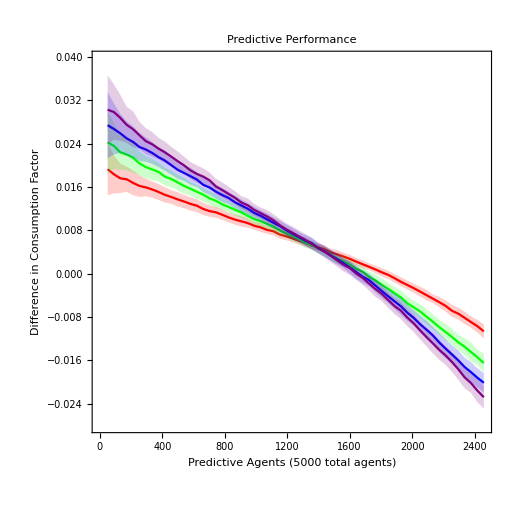

```mathematica
ratio=0.5;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
Show[
(* The plot *)
ListPlotError[{pdt03,pdt05,pdt08,pdt10},{pdt03e,pdt05e,pdt08e,pdt10e},PlotStyle->{Red,Green,Blue,Purple},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents (5000 total agents)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Predictive Performance",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Predictive, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Predictive, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}]
],Scaled[{0.8,0.8}]]
(* End of the Legends *)
]
```

```mathematica
ratio=1;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
plot=Show[
(* The plot *)
ListPlotError[{pdt03,pdt05,pdt08,pdt10},{pdt03e,pdt05e,pdt08e,pdt10e},PlotStyle->{Red,Green,Blue,Purple},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents (5000 total agents)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Predictive Performance",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Predictive, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Predictive, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}]
],Scaled[{0.8,0.8}]]
(* End of the Legends *)
];
```

```mathematica
Export["Predictive_T0.jpg",plot,"CompressionLevel"->0];
```

#### Gradient agents

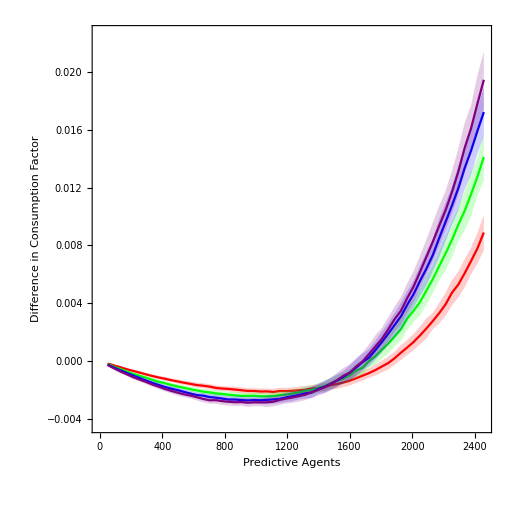

```mathematica
ratio=0.5;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
Show[
(* The plot *)
ListPlotError[{gdt03,gdt05,gdt08,gdt10},{gdt03e,gdt05e,gdt08e,gdt10e},PlotStyle->{Red,Green,Blue,Purple},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Gradient, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Gradient, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Gradient, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}],Background->White],Scaled[{0.2,0.8}]]
(* End of the Legends *)
]
```

```mathematica
ratio=1;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
plot=Show[
(* The plot *)
ListPlotError[{gdt03,gdt05,gdt08,gdt10},{gdt03e,gdt05e,gdt08e,gdt10e},PlotStyle->{Red,Green,Blue,Purple},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents (5000 total agents)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Gradient Performance",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Gradient, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Gradient, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Gradient, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}],Background->White
],Scaled[{0.2,0.8}]]
(* End of the Legends *)
];
```

```mathematica
Export["Gradient_T0.jpg",plot,"CompressionLevel"->0];
```

#### Predictive and Gradient agents - no error shown

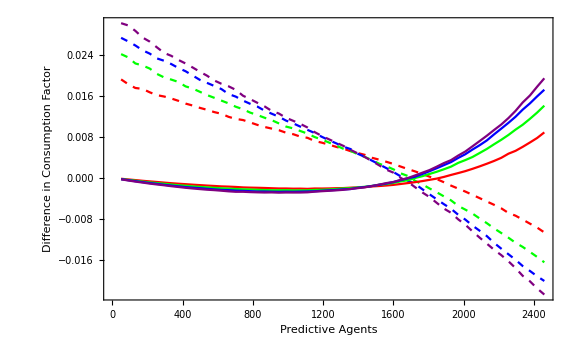

```mathematica
ListLinePlot[{pdt03,pdt05,pdt08,pdt10,gdt03,gdt05,gdt08,gdt10},Frame->True,FrameLabel->{Style["Predictive Agents",12,FontFamily->"Arial"],Style["Difference in Consumption Factor",12,FontFamily->"Arial"]},PlotStyle->{{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Dashed,Purple},Red,Green,Blue,Purple},ImageSize->Large]
```

```mathematica
(*plot=ListLinePlot[{pdt03,pdt05,pdt08,pdt10,gdt03,gdt05,gdt08,gdt10},Frame->True,FrameLabel->{Style["Predictive Agents",12,FontFamily->"Arial"],Style["Difference in Consumption Factor",12,FontFamily->"Arial"]},PlotStyle->{{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Dashed,Purple},Red,Green,Blue,Purple},ImageSize->resolution,AspectRatio->1];*)
```

```mathematica
(*Export["PvNP_T0.jpg",plot,"CompressionLevel"->0];*)
```

### With error

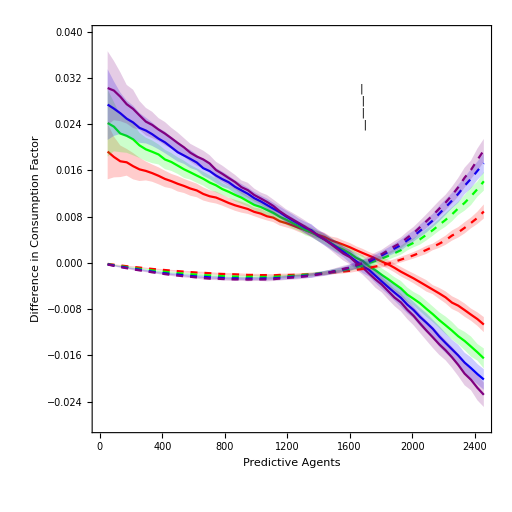

```mathematica
ratio=0.5;
fontSize=20*ratio*0.7;
lineSize=50*ratio*0.7;
labelFont=24*ratio;
Show[
(* The plot *)
ListPlotError[{pdt03,pdt05,pdt08,pdt10,gdt03,gdt05,gdt08,gdt10},{pdt03e,pdt05e,pdt08e,pdt10e,gdt03e,gdt05e,gdt08e,gdt10e},PlotStyle->{Red,Green,Blue,Purple,{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Purple,Dashed}},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Multicolumn[{
LineLegend[{Red},     {"  Predictive, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Predictive, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Red,Dashed],Dashed},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Green,Dashed]},{"  Gradient, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Blue,Dashed]},{"  Gradient, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Purple,Dashed]},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
},2],Background->White],Scaled[{0.68,0.8}]]
(* End of the Legends *)
]
```

```mathematica
ratio=1.;
fontSize=20*ratio*0.7;
lineSize=50*ratio*0.7;
labelFont=24*ratio;
plot=Show[
(* The plot *)
ListPlotError[{pdt03,pdt05,pdt08,pdt10,gdt03,gdt05,gdt08,gdt10},{pdt03e,pdt05e,pdt08e,pdt10e,gdt03e,gdt05e,gdt08e,gdt10e},PlotStyle->{Red,Green,Blue,Purple,{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Purple,Dashed}},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents (5000 total agents)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Population Performance (Predictive and Gradient)",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Multicolumn[{
LineLegend[{Red},     {"  Predictive, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Predictive, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Red,Dashed]},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Green,Dashed]},{"  Gradient, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Blue,Dashed]},{"  Gradient, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Purple,Dashed]},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
},2],Background->White],Scaled[{0.68,0.8}]]
(* End of the Legends *)
];
```

```mathematica
Export["PvNP_T0.jpg",plot,"CompressionLevel"->0];
```

# Get data for T=0.5

#### Get data

```mathematica
pdt03=GetFileData["PvNP_tau0.03_num5000_vel1_T0.5","PDiff"];
gdt03=GetFileData["PvNP_tau0.03_num5000_vel1_T0.5","GDiff"];
pdt05=GetFileData["PvNP_tau0.05_num5000_vel1_T0.5","PDiff"];
gdt05=GetFileData["PvNP_tau0.05_num5000_vel1_T0.5","GDiff"];
pdt08=GetFileData["PvNP_tau0.08_num5000_vel1_T0.5","PDiff"];
gdt08=GetFileData["PvNP_tau0.08_num5000_vel1_T0.5","GDiff"];
pdt10=GetFileData["PvNP_tau0.1_num5000_vel1_T0.5","PDiff"];
gdt10=GetFileData["PvNP_tau0.1_num5000_vel1_T0.5","GDiff"];
```

#### Get error

```mathematica
pdt03e=GetFileError["PvNP_tau0.03_num5000_vel1_T0.5","PDiff"];
gdt03e=GetFileError["PvNP_tau0.03_num5000_vel1_T0.5","GDiff"];
pdt05e=GetFileError["PvNP_tau0.05_num5000_vel1_T0.5","PDiff"];
gdt05e=GetFileError["PvNP_tau0.05_num5000_vel1_T0.5","GDiff"];
pdt08e=GetFileError["PvNP_tau0.08_num5000_vel1_T0.5","PDiff"];
gdt08e=GetFileError["PvNP_tau0.08_num5000_vel1_T0.5","GDiff"];
pdt10e=GetFileError["PvNP_tau0.1_num5000_vel1_T0.5","PDiff"];
gdt10e=GetFileError["PvNP_tau0.1_num5000_vel1_T0.5","GDiff"];
```

#### Plot

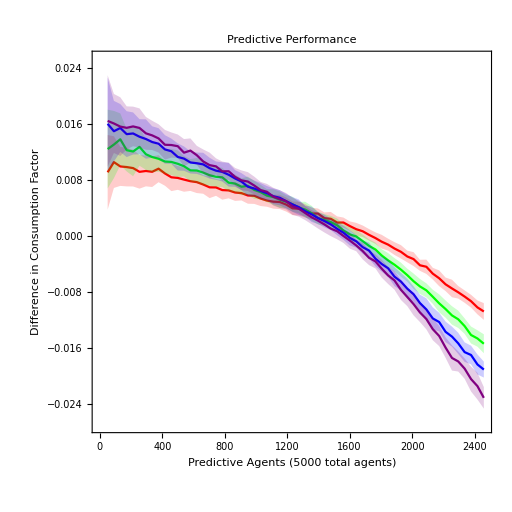

```mathematica
ratio=0.5;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
Show[
(* The plot *)
ListPlotError[{pdt03,pdt05,pdt08,pdt10},{pdt03e,pdt05e,pdt08e,pdt10e},PlotStyle->{Red,Green,Blue,Purple},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents (5000 total agents)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Predictive Performance",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Predictive, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Predictive, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}]
],Scaled[{0.8,0.8}]]
(* End of the Legends *)
]
```

```mathematica
ratio=1;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
plot=Show[
(* The plot *)
ListPlotError[{pdt03,pdt05,pdt08,pdt10},{pdt03e,pdt05e,pdt08e,pdt10e},PlotStyle->{Red,Green,Blue,Purple},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents (5000 total agents)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Predictive Performance",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Predictive, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Predictive, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}]
],Scaled[{0.8,0.8}]]
(* End of the Legends *)
];
```

```mathematica
Export["Predictive_T0.5.jpg",plot,"CompressionLevel"->0];
```

#### Gradient agents

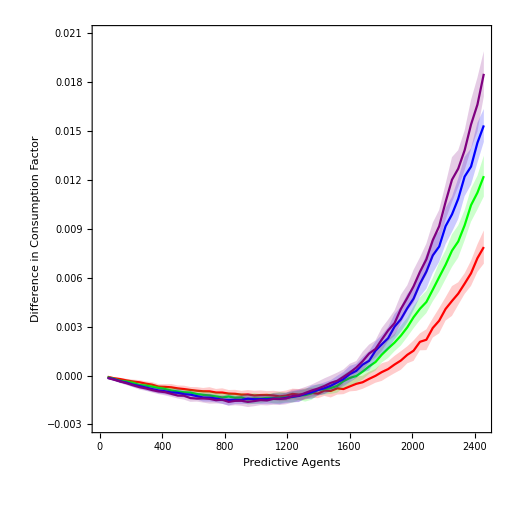

```mathematica
ratio=0.5;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
Show[
(* The plot *)
ListPlotError[{gdt03,gdt05,gdt08,gdt10},{gdt03e,gdt05e,gdt08e,gdt10e},PlotStyle->{Red,Green,Blue,Purple},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Gradient, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Gradient, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Gradient, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}],Background->White],Scaled[{0.2,0.8}]]
(* End of the Legends *)
]
```

```mathematica
ratio=1;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
plot=Show[
(* The plot *)
ListPlotError[{gdt03,gdt05,gdt08,gdt10},{gdt03e,gdt05e,gdt08e,gdt10e},PlotStyle->{Red,Green,Blue,Purple},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents (5000 total agents)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Gradient Performance",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Gradient, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Gradient, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Gradient, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}],Background->White
],Scaled[{0.2,0.8}]]
(* End of the Legends *)
];
```

```mathematica
Export["Gradient_T0.5.jpg",plot,"CompressionLevel"->0];
```

#### Predictive and Gradient agents - no error shown

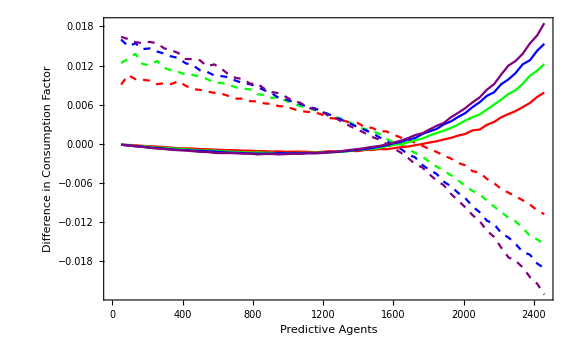

```mathematica
ListLinePlot[{pdt03,pdt05,pdt08,pdt10,gdt03,gdt05,gdt08,gdt10},Frame->True,FrameLabel->{Style["Predictive Agents",12,FontFamily->"Arial"],Style["Difference in Consumption Factor",12,FontFamily->"Arial"]},PlotStyle->{{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Dashed,Purple},Red,Green,Blue,Purple},ImageSize->Large]
```

```mathematica
plot=ListLinePlot[{pdt03,pdt05,pdt08,pdt10,gdt03,gdt05,gdt08,gdt10},Frame->True,FrameLabel->{Style["Predictive Agents",12,FontFamily->"Arial"],Style["Difference in Consumption Factor",12,FontFamily->"Arial"]},PlotStyle->{{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Dashed,Purple},Red,Green,Blue,Purple},ImageSize->resolution,AspectRatio->1];
```

```mathematica
(*Export["PvNP_T0.5.jpg",plot,"CompressionLevel"->0];*)
```

### With error

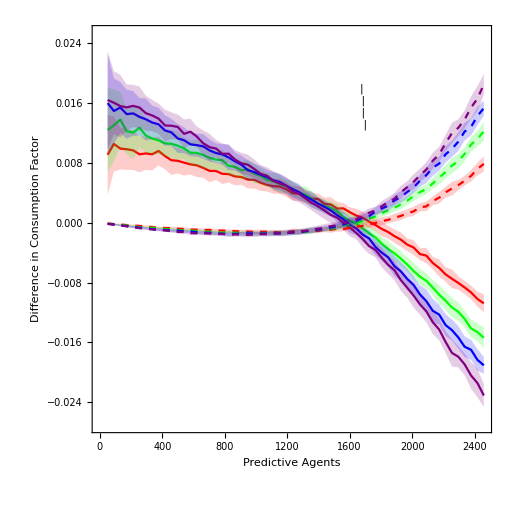

```mathematica
ratio=0.5;
fontSize=20*ratio*0.7;
lineSize=50*ratio*0.7;
labelFont=24*ratio;
Show[
(* The plot *)
ListPlotError[{pdt03,pdt05,pdt08,pdt10,gdt03,gdt05,gdt08,gdt10},{pdt03e,pdt05e,pdt08e,pdt10e,gdt03e,gdt05e,gdt08e,gdt10e},PlotStyle->{Red,Green,Blue,Purple,{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Purple,Dashed}},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Multicolumn[{
LineLegend[{Red},     {"  Predictive, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Predictive, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Red,Dashed],Dashed},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Green,Dashed]},{"  Gradient, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Blue,Dashed]},{"  Gradient, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Purple,Dashed]},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
},2],Background->White],Scaled[{0.68,0.8}]]
(* End of the Legends *)
]
```

```mathematica
ratio=1.;
fontSize=20*ratio*0.7;
lineSize=50*ratio*0.7;
labelFont=24*ratio;
plot=Show[
(* The plot *)
ListPlotError[{pdt03,pdt05,pdt08,pdt10,gdt03,gdt05,gdt08,gdt10},{pdt03e,pdt05e,pdt08e,pdt10e,gdt03e,gdt05e,gdt08e,gdt10e},PlotStyle->{Red,Green,Blue,Purple,{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Purple,Dashed}},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents (5000 total agents)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Population Performance (Predictive and Gradient)",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Multicolumn[{
LineLegend[{Red},     {"  Predictive, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Predictive, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Red,Dashed]},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Green,Dashed]},{"  Gradient, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Blue,Dashed]},{"  Gradient, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Purple,Dashed]},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
},2],Background->White],Scaled[{0.68,0.8}]]
(* End of the Legends *)
];
```

```mathematica
Export["PvNP_T0.5.jpg",plot,"CompressionLevel"->0];
```

# Get data for T=1

#### Get data

```mathematica
pdt03=GetFileData["PvNP_tau0.03_num5000_vel1_T1","PDiff"];
gdt03=GetFileData["PvNP_tau0.03_num5000_vel1_T1","GDiff"];
pdt05=GetFileData["PvNP_tau0.05_num5000_vel1_T1","PDiff"];
gdt05=GetFileData["PvNP_tau0.05_num5000_vel1_T1","GDiff"];
pdt08=GetFileData["PvNP_tau0.08_num5000_vel1_T1","PDiff"];
gdt08=GetFileData["PvNP_tau0.08_num5000_vel1_T1","GDiff"];
pdt10=GetFileData["PvNP_tau0.1_num5000_vel1_T1","PDiff"];
gdt10=GetFileData["PvNP_tau0.1_num5000_vel1_T1","GDiff"];
```

#### Get error

```mathematica
pdt03e=GetFileError["PvNP_tau0.03_num5000_vel1_T1","PDiff"];
gdt03e=GetFileError["PvNP_tau0.03_num5000_vel1_T1","GDiff"];
pdt05e=GetFileError["PvNP_tau0.05_num5000_vel1_T1","PDiff"];
gdt05e=GetFileError["PvNP_tau0.05_num5000_vel1_T1","GDiff"];
pdt08e=GetFileError["PvNP_tau0.08_num5000_vel1_T1","PDiff"];
gdt08e=GetFileError["PvNP_tau0.08_num5000_vel1_T1","GDiff"];
pdt10e=GetFileError["PvNP_tau0.1_num5000_vel1_T1","PDiff"];
gdt10e=GetFileError["PvNP_tau0.1_num5000_vel1_T1","GDiff"];
```

#### Plot

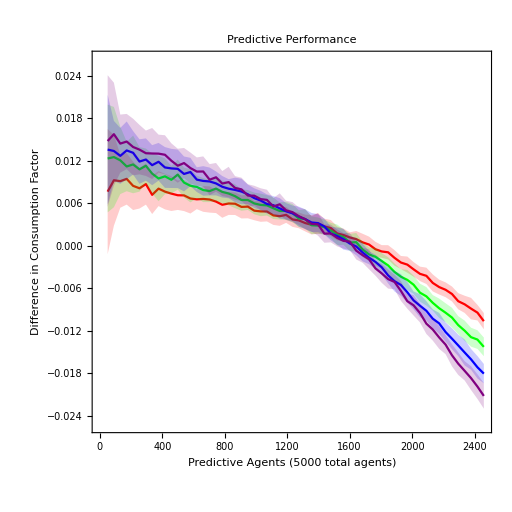

```mathematica
ratio=0.5;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
Show[
(* The plot *)
ListPlotError[{pdt03,pdt05,pdt08,pdt10},{pdt03e,pdt05e,pdt08e,pdt10e},PlotStyle->{Red,Green,Blue,Purple},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents (5000 total agents)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Predictive Performance",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Predictive, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Predictive, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}]
],Scaled[{0.8,0.8}]]
(* End of the Legends *)
]
```

```mathematica
ratio=1;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
plot=Show[
(* The plot *)
ListPlotError[{pdt03,pdt05,pdt08,pdt10},{pdt03e,pdt05e,pdt08e,pdt10e},PlotStyle->{Red,Green,Blue,Purple},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents (5000 total agents)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Predictive Performance",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Predictive, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Predictive, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}]
],Scaled[{0.8,0.8}]]
(* End of the Legends *)
];
```

```mathematica
Export["Predictive_T1.jpg",plot,"CompressionLevel"->0];
```

#### Gradient agents

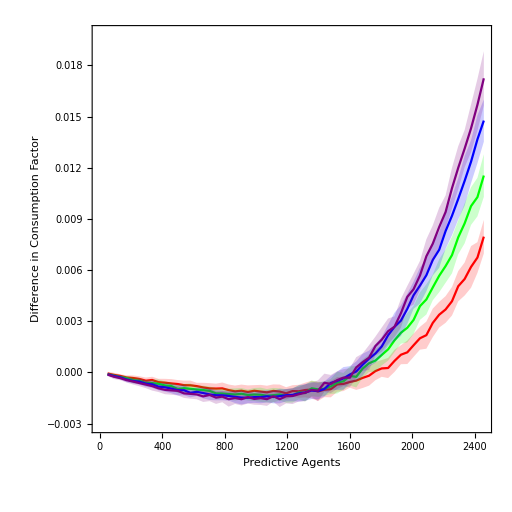

```mathematica
ratio=0.5;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
Show[
(* The plot *)
ListPlotError[{gdt03,gdt05,gdt08,gdt10},{gdt03e,gdt05e,gdt08e,gdt10e},PlotStyle->{Red,Green,Blue,Purple},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Gradient, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Gradient, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Gradient, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}],Background->White],Scaled[{0.2,0.8}]]
(* End of the Legends *)
]
```

```mathematica
ratio=1;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
plot=Show[
(* The plot *)
ListPlotError[{gdt03,gdt05,gdt08,gdt10},{gdt03e,gdt05e,gdt08e,gdt10e},PlotStyle->{Red,Green,Blue,Purple},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents (5000 total agents)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Gradient Performance",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Gradient, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Gradient, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Gradient, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}],Background->White
],Scaled[{0.2,0.8}]]
(* End of the Legends *)
];
```

```mathematica
Export["Gradient_T1.jpg",plot,"CompressionLevel"->0];
```

#### Predictive and Gradient agents - no error shown

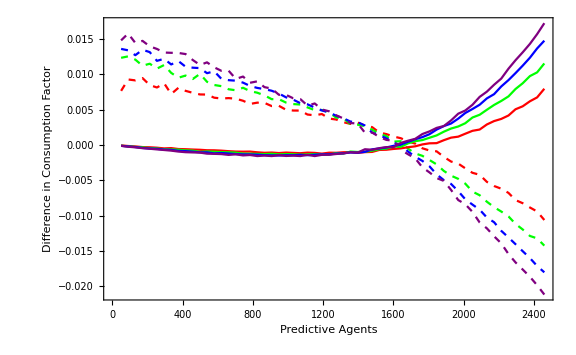

```mathematica
ListLinePlot[{pdt03,pdt05,pdt08,pdt10,gdt03,gdt05,gdt08,gdt10},Frame->True,FrameLabel->{Style["Predictive Agents",12,FontFamily->"Arial"],Style["Difference in Consumption Factor",12,FontFamily->"Arial"]},PlotStyle->{{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Dashed,Purple},Red,Green,Blue,Purple},ImageSize->Large]
```

```mathematica
plot=ListLinePlot[{pdt03,pdt05,pdt08,pdt10,gdt03,gdt05,gdt08,gdt10},Frame->True,FrameLabel->{Style["Predictive Agents",12,FontFamily->"Arial"],Style["Difference in Consumption Factor",12,FontFamily->"Arial"]},PlotStyle->{{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Dashed,Purple},Red,Green,Blue,Purple},ImageSize->resolution,AspectRatio->1];
```

```mathematica
(*Export["PvNP_T0.5.jpg",plot,"CompressionLevel"->0];*)
```

### With error

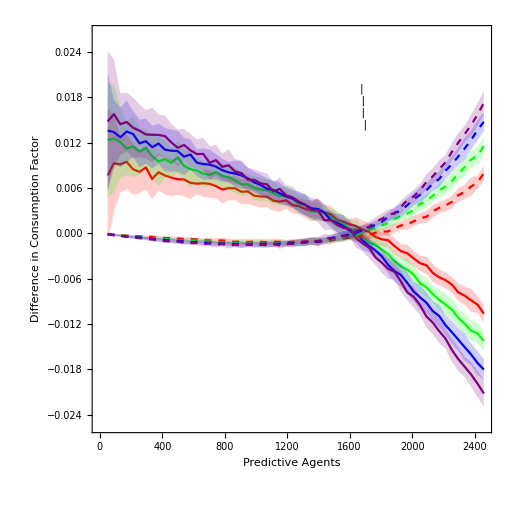

```mathematica
ratio=0.5;
fontSize=20*ratio*0.7;
lineSize=50*ratio*0.7;
labelFont=24*ratio;
Show[
(* The plot *)
ListPlotError[{pdt03,pdt05,pdt08,pdt10,gdt03,gdt05,gdt08,gdt10},{pdt03e,pdt05e,pdt08e,pdt10e,gdt03e,gdt05e,gdt08e,gdt10e},PlotStyle->{Red,Green,Blue,Purple,{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Purple,Dashed}},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Multicolumn[{
LineLegend[{Red},     {"  Predictive, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Predictive, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Red,Dashed],Dashed},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Green,Dashed]},{"  Gradient, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Blue,Dashed]},{"  Gradient, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Purple,Dashed]},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
},2],Background->White],Scaled[{0.68,0.8}]]
(* End of the Legends *)
]
```

```mathematica
ratio=1.;
fontSize=20*ratio*0.7;
lineSize=50*ratio*0.7;
labelFont=24*ratio;
plot=Show[
(* The plot *)
ListPlotError[{pdt03,pdt05,pdt08,pdt10,gdt03,gdt05,gdt08,gdt10},{pdt03e,pdt05e,pdt08e,pdt10e,gdt03e,gdt05e,gdt08e,gdt10e},PlotStyle->{Red,Green,Blue,Purple,{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Purple,Dashed}},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents (5000 total agents)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Population Performance (Predictive and Gradient)",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Multicolumn[{
LineLegend[{Red},     {"  Predictive, τ=0.03"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Predictive, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Red,Dashed]},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Green,Dashed]},{"  Gradient, τ=0.05"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Blue,Dashed]},{"  Gradient, τ=0.08"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Directive[Purple,Dashed]},{"  Gradient, τ=0.10"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
},2],Background->White],Scaled[{0.68,0.8}]]
(* End of the Legends *)
];
```

```mathematica
Export["PvNP_T1.jpg",plot,"CompressionLevel"->0];
```

# Compair different temperatures

#### Get data

```mathematica
pdt03T0=GetFileData["PvNP_tau0.03_num5000_vel1","PDiff"];
pdt03T5=GetFileData["PvNP_tau0.03_num5000_vel1_T0.5","PDiff"];
pdt03T10=GetFileData["PvNP_tau0.03_num5000_vel1_T1","PDiff"];
```

#### Get error

```mathematica
pdt03eT0=GetFileError["PvNP_tau0.03_num5000_vel1","PDiff"];
pdt03eT5=GetFileError["PvNP_tau0.03_num5000_vel1_T0.5","PDiff"];
pdt03eT10=GetFileError["PvNP_tau0.03_num5000_vel1_T1","PDiff"];
```

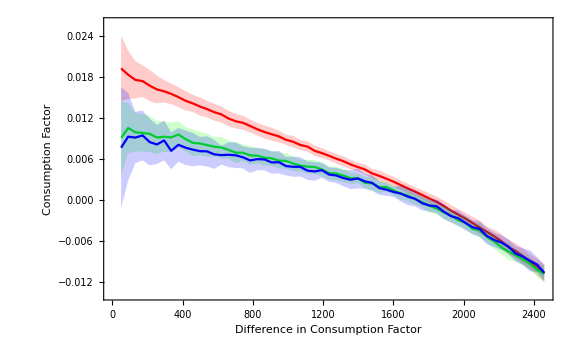

```mathematica
ListPlotError[{pdt03T0,pdt03T5,pdt03T10},{pdt03eT0,pdt03eT5,pdt03eT10},PlotStyle->{Red,Green,Blue},Frame->True,FrameLabel->{Style["Difference in Consumption Factor",12,FontFamily->"Arial"],Style["Consumption Factor",12,FontFamily->"Arial"]},ImageSize->Large]
```

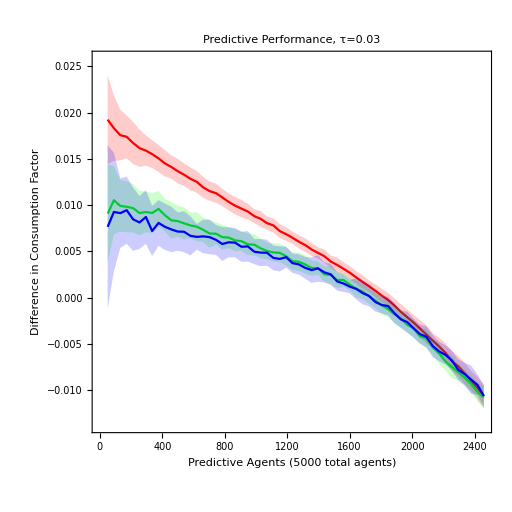

```mathematica
ratio=0.5;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
Show[
(* The plot *)
ListPlotError[{pdt03T0,pdt03T5,pdt03T10},{pdt03eT0,pdt03eT5,pdt03eT10},PlotStyle->{Red,Green,Blue},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictive Agents (5000 total agents)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Predictive Performance, τ=0.03",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Predictive, T=0"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive, T=0.5"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive, T=1.0"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}]
],Scaled[{0.8,0.8}]]
(* End of the Legends *)
]
```

# Get CF vs Consumption Data

```mathematica
Header="CFvsConsumption_num5000_frac0.2_vel1";
```

```mathematica
pcvc=GetFileData[Header,"PCF"];
pcvce=GetFileError[Header,"PCF"];
gcvc=GetFileData[Header,"GCF"];
gcvce=GetFileError[Header,"GCF"];
```

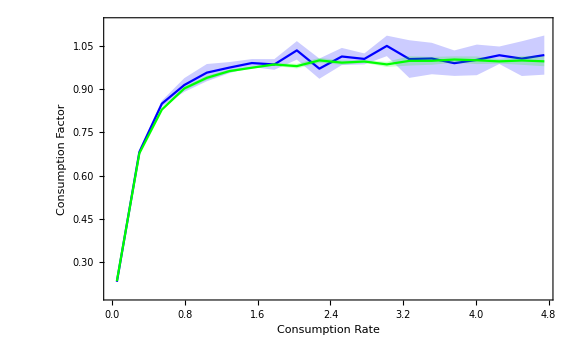

```mathematica
ListPlotError[{pcvc,gcvc},{pcvce,gcvce},PlotStyle->{Blue,Green},Frame->True,FrameLabel->{Style["Consumption Rate",12,FontFamily->"Arial"],Style["Consumption Factor",12,FontFamily->"Arial"]},ImageSize->Large]
```